THE  GOMPERTZ  SOFTWARE RELIABILITY MODEL

```mathematica
j1 =Import["/Users/olegzaim/Downloads/Верефикация и Валидиране на Софтуер/FMI-SE-4-2-Software_Reliability-master/J1_data.csv"];
Manipulate[
Dynamic@Show[Plot[f[t], {t, 1,62},(* функция на времето на изпитване *)
LabelStyle-> Directive[Green, Bold], (* форматиране на динамичната графика*)
PlotLabel -> 133* Exp[-α*Exp[-β*t]]],
ListPlot[ j1,
PlotStyle-> Red,
PlotMarkers -> {Automatic,Small}],
PlotRange -> {Automatic, {0,133}},
AxesOrigin -> {0,0}], 
{{α,0}, 0,10, Appearance -> "Open" },
{{β,0}, 0.01,10, Appearance -> "Open" },
Initialization :> (f[t_]:= 140*Exp[-α*Exp[-β*t]])
]
```

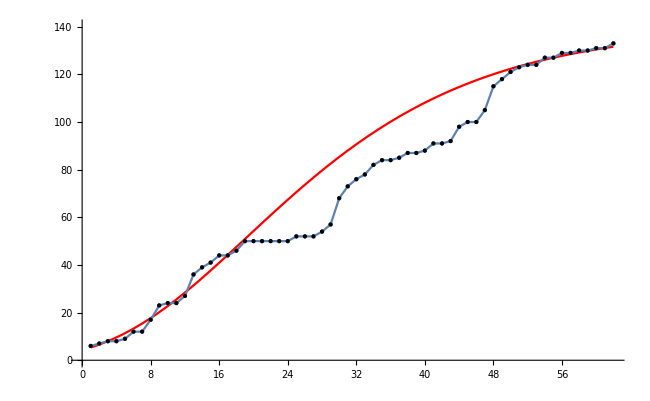

```mathematica
α = 3.48;
β = 0.065;
f[t_]:= 140*Exp[-α*Exp[-β*t]];
linechart = Plot[f[t], {t, 1,62},Epilog->Map[Point, j1],  PlotStyle->{Red}, PlotRange -> {0,140}]; 
Show[linechart, ListPlot[j1, Joined-> True, Mesh->Full, MeshStyle-> Directive[PointSize[Large], Thick]]]
```

```mathematica
ClearAll;
j4 =Import["/Users/olegzaim/Downloads/Верефикация и Валидиране на Софтуер/FMI-SE-4-2-Software_Reliability-master/J4_data.csv"];
Manipulate[
Dynamic@Show[Plot[f[t], {t, 1,112},(* функция на времето на изпитване *)
LabelStyle-> Directive[Green, Bold], (* форматиране на динамичната графика*)
PlotLabel -> 183* Exp[-α*Exp[-β*t]]],
ListPlot[ j4,
PlotStyle-> Red,
PlotMarkers -> {Automatic,Small}],
PlotRange -> {Automatic, {0,185}},
AxesOrigin -> {0,0}], 
{{α,0}, 0,20, Appearance -> "Open" },
{{β,0}, 0.01,10, Appearance -> "Open" },
Initialization :> (f[t_]:= 183*Exp[-α*Exp[-β*t]])
]
```

```mathematica
|
```

```mathematica
α = 9.14;
β = 0.065;
f[t_]:= 183*Exp[-α*Exp[-β*t]];
j4 =Import["/Users/olegzaim/Downloads/Верефикация и Валидиране на Софтуер/FMI-SE-4-2-Software_Reliability-master/J4_data.csv"];
linechart = Plot[f[t], {t, 1,112},Epilog->Map[Point, j4],  PlotStyle->{Red}, PlotRange -> {0,183}]; 
Show[linechart, ListPlot[j4, Joined-> True, Mesh->Full, MeshStyle-> Directive[PointSize[Large], Thick]]]
```

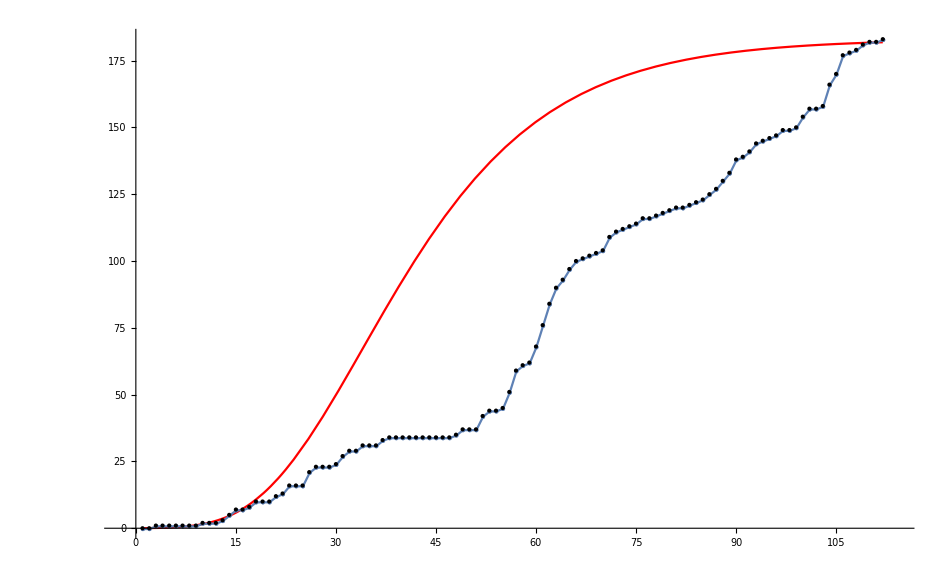

```mathematica
Song, Cheng - Pham software reliability model
```

a (1-β/(β+Log[(a+ⅇ^(b t))/(1+a)]))^α

140

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{b→1.20336,α→49.3467,β→0.353559}

0.35

49.34

140

1.2

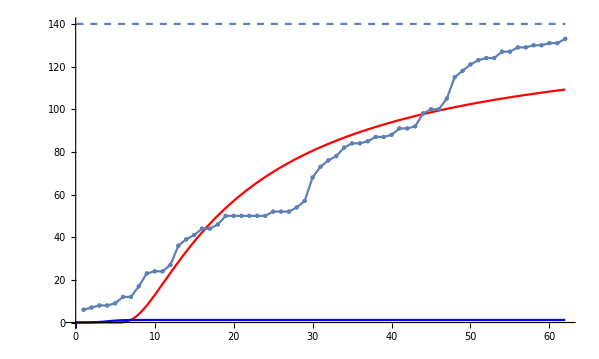

```mathematica
j1 =Import["/Users/olegzaim/Downloads/Верефикация и Валидиране на Софтуер/FMI-SE-4-2-Software_Reliability-master/J1_data.csv"];
Clear[β]
Clear[b]
Clear[a]
Clear[α]
Manipulate[Show[ListLinePlot[j1],Plot[a*(1-β/(β+Log[(a+Exp[b*t])/(a+1)]))^α,{t,0,62},PlotStyle->Red]],{α, 0.01, 50}, {β, 0.01, 2}, {a, 100, 400},{ b, 0.01, 2}]
modelmodel= a*(1-β/(β+Log[(a+Exp[b*t])/(a+1)]))^α
a= 140
fitfit = FindFit[j1, modelmodel ,{b,α,β}, t]
β=0.35
α=49.34
a= 140
b=1.20
H[t_]:=a*(1-β/(β+Log[(a+Exp[b*t])/(a+1)]))^α
H1[t_]:=b/(1+a*Exp[-b*t])
H2[t_]:=a
g1=Plot[H[t],{t,0,62},PlotRange->{0,140},AspectRatio->0.6,PlotStyle->{Red}];
g2=Plot[H1[t],{t,0, 62},PlotRange->{0,140},AspectRatio->0.6,PlotStyle->{Blue}];
g3=Plot[H2[t],{t,0.1,62},PlotRange->{0,140},AspectRatio->0.6,PlotStyle->{Dashed}];
Show[g1,g2,g3, ListPlot[j1, Joined -> True, Mesh -> Full, MeshStyle-> Directive[PointSize[Large], Thick]]]
```

140

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{b→1.20336,α→49.3467,β→0.353559}

0.3535

49.346

140

1.203

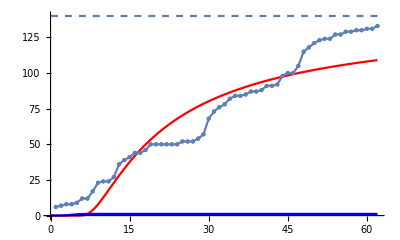

140

1.203

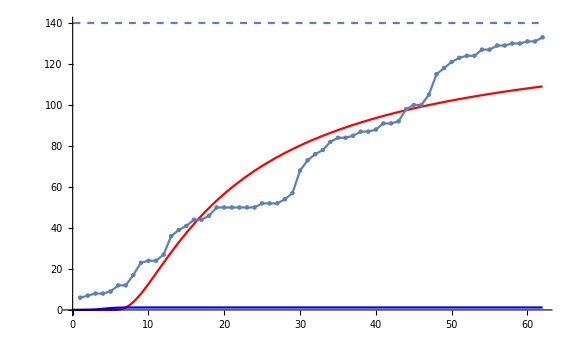

```mathematica
{a (1-β/(β+ln[(a+ⅇ^(b t))/(1+a)]))^α}
```

a (1-β/(β+Log[(a+ⅇ^(b t))/(1+a)]))^α

198

{b→0.0534186,α→1.02897,β→0.185076}

0.18

1.028

198

0.053

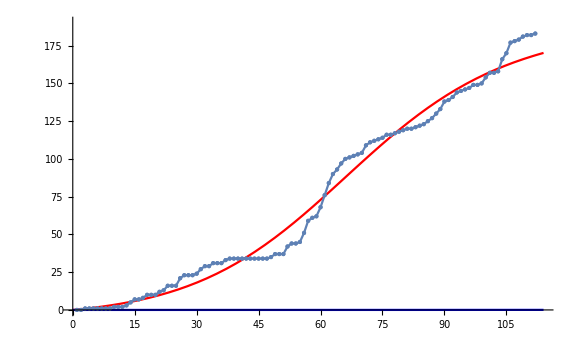

```mathematica
j4 =Import["/Users/olegzaim/Downloads/Верефикация и Валидиране на Софтуер/FMI-SE-4-2-Software_Reliability-master/J4_data.csv"];
Clear[β]
Clear[b]
Clear[a]
Clear[α]
modelmodel= a*(1-β/(β+Log[(a+Exp[b*t])/(a+1)]))^α
a= 198
fitfit = FindFit[j4, modelmodel ,{b,α,β}, t]
β=0.18
α=1.028
a= 198
b=0.053
H[t_]:=a*(1-β/(β+Log[(a+Exp[b*t])/(a+1)]))^α
H1[t_]:=b/(1+a*Exp[-b*t])
H2[t_]:=a
g1=Plot[H[t],{t,0,114},PlotRange->{0,190},AspectRatio->0.6,PlotStyle->{Red}];
g2=Plot[H1[t],{t,0, 114},PlotRange->{0,190},AspectRatio->0.6,PlotStyle->{Blue}];
g3=Plot[H2[t],{t,0.1,114},PlotRange->{0,190},AspectRatio->0.6,PlotStyle->{Dashed}];
Show[g1,g2,g3, ListPlot[j4, Joined -> True, Mesh -> Full, MeshStyle-> Directive[PointSize[Large], Thick]]]
```

-61.93

53.23

200

10.4

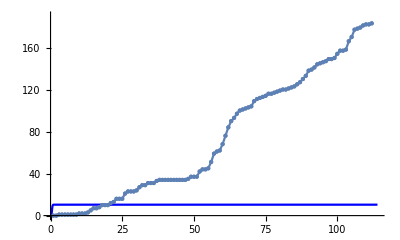

```mathematica
{b->6.868124382864541,α->5.045557043619032,β->5.045704973176119}
```